# Mathematica code for implementation of the reduced model for facultative syntrophy

This notebook contains source code for the following preprint article:

Droste MJ, Planqué R, Bruggeman FJ (2026) Emergent metabolic cooperation in communities of microbes that maximise growth rate by optimal protein expression.

Short description
This code contains the implementation of the reduced model for facultative syntrophy, where we assume the consuming species to be a passive consumer of the exchange metabolite P_1. This assumption allows for direct perturbation of the P_1 concentration, and reduces the coupled optimisation problem for the community growth rate of a two-species community to a single-species optimisation problem. For this reduced model we show that a switch from metabolic mode 2 to mode 1 occurs as the P_1 concentration decreases.
More information on the implementation of the reduced model and facultative syntrophy can be found in the Supplementary Appendices of the article.

#### Settings for figures

```mathematica
SetOptions[{Plot,ListPlot,ListLogPlot,ListLinePlot,ListLinePlot,LogLinearPlot},PlotStyle->Black,Frame->True,ImageSize->550,BaseStyle->{FontSize->22,FontColor->Black},FrameStyle->Directive[Black,22,Thickness->0.005], PlotStyle->ColorData[68,"ColorList"],AspectRatio->1,Prolog->{-Graphics-,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];
```

#### Rate equations and model parameters

```mathematica
v[kcat_,s1_,s2_,e_,K1_,K2_,Keq_]:=kcat(e s1/K1(1-s2/(s1 Keq)))/(1+s1/K1+s2/K2)
```

```mathematica
vT=v[kT,s,sA,eT,1,2,KeqT];
v2=v[k2,sA,p2,e2,2,1,Keq];
v1=v[k1,sA,p1,e1,2,0.01,Keq];
vR=kR fR eR;
```

```mathematica
ParamsFacSynRed={s->0.3,p2->0.5,
Keq->10,KeqT->1,
m2->2,m1->1,mR->700,
fR->0.8,YsaR->200,
eTot->1,eT->0.1,
kR->0.089,k2->185,k1->1000,kT->1000};
```

#### Optimisation problem: Maximise the growth rate of the producer for varying concentrations of P_1

```mathematica
ModelEquationsJoinedFacSynRed[P1v_]:=Join[{Evaluate[vR/eTot]},
{(*Positivity constraints*)sA>=0,e2>=0,e1>=0,eR>=0,
(*Enzyme constraints*)eT+e2+e1+eR<=eTot,
(*Steady states*)vT==v1+v2+YsaR vR,mR vR==m2 v2 + m1 v1}]/.{p1->P1v}
OptimisationProblemFuncFacSynRed[P1v_]:=NMaximize[ModelEquationsJoinedFacSynRed[P1v]/.ParamsFacSynRed,{sA,e2,e1,eR}]
```

#### Results and figures

We run the optimisation problem for different values of the P_1 concentration. After obtaining the results, we normalise the P_1 concentration and the growth rate relative to the population containing only the producer.

```mathematica
p1start=0.005;
p1end=0.045;
p1step=0.002;
OptimisationProblemSolFacSynRed=Table[{p1->p1val,λ->OptimisationProblemFuncFacSynRed[p1val][[1]],OptimisationProblemFuncFacSynRed[p1val][[2]]}//Flatten,{p1val,p1start,p1end,p1step}];
```

```mathematica
p1switchFacSynRed=p1/.First@Select[OptimisationProblemSolFacSynRed,(e2/. #)>0.0001&];
λswitchFacSynRed=λ/.First@Select[OptimisationProblemSolFacSynRed,(e2/. #)>0.0001&];
```

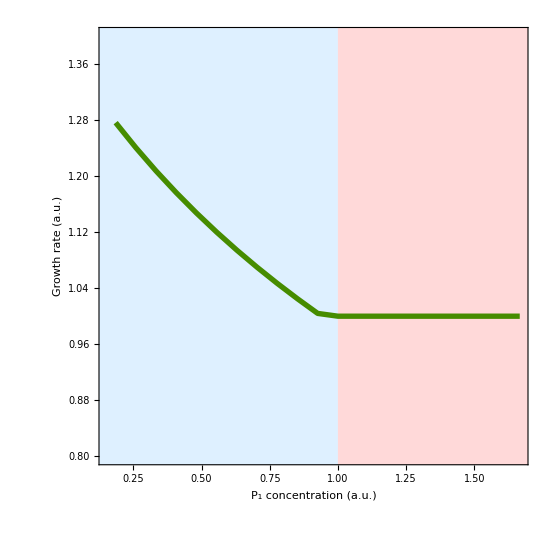

```mathematica
ListLinePlot[{p1/p1switchFacSynRed,λ/λswitchFacSynRed}/.OptimisationProblemSolFacSynRed,FrameLabel->{ "P_1 concentration (a.u.)","Growth rate (a.u.)"},PlotRange->{All,{0.8,1.4}},PlotStyle->{ColorData[68,"ColorList"][[3]],Thickness[0.007]},Prolog->{{LightBlue,Rectangle[{-1,-1},{1,2}]},{LightRed,Rectangle[{1,-1},{8,2}]}}]
```